```mathematica
f[n_,t_] := Sum[ (-1)^(k+1)/k  (-1)^k(1-Gamma[k,-Log[100]]/Gamma[k]),{k,1,t}]
```

```mathematica
N[f[100,10000]]+Log[Log[100]]+EulerGamma
```

30.1261-2.09386×10^-14 ⅈ

```mathematica
N[ExpIntegralEi[Log[100]]]
```

30.1261

```mathematica
f2[n_,t_,s_] := Sum[ (-1)^(k+1)/k  (-1)^k(1-Gamma[k,-(s)Log[100]]/Gamma[k]),{k,1,t}]
```

```mathematica
f2a[n_,t_,s_,s2_] := Sum[ (-1)^(k+1)/k  (-1)^k((1-Gamma[k,-s Log[100]]/Gamma[k])+(1-Gamma[k,-s2 Log[100]]/Gamma[k])),{k,1,t}]
```

```mathematica
N[f2[100,1000,2]]+Log[2Log[100]]+EulerGamma
```

1246.14-1.13248×10^-9 ⅈ

```mathematica
N[ExpIntegralEi[2 Log[100]]]
```

1246.14

```mathematica
N[f2[100,1000,3]]+Log[3Log[100]]+EulerGamma
```

78627.5+9.32697×10^-6 ⅈ

```mathematica
N[ExpIntegralEi[3 Log[100]]]
```

78627.5

```mathematica
N[f2a[100,1600,ZetaZero[1],ZetaZero[-1]]]+Log[(ZetaZero[1]+ZetaZero[-1])Log[100]]+EulerGamma
```

1.88143×10^12+0. ⅈ

```mathematica
N[ExpIntegralEi[(ZetaZero[1]) Log[100]]+ExpIntegralEi[(ZetaZero[-1]) Log[100]]]
```

0.232873+0. ⅈ

```mathematica
N[ZetaZero[1]]
```

0.5+14.1347 ⅈ

```mathematica
Table[ {k,N[(-1)^(k+1)/k  (-1)^k(1-Gamma[k,-(s)Log[100]]/Gamma[k])]},{k,1,200}]/.s->ZetaZero[1]//TableForm
```

1 | -7.36665+7.71141 ⅈ
2 | 254.625+202.189 ⅈ
3 | 4274.85-5622.11 ⅈ
4 | -92840.2-67705.8 ⅈ
5 | -856579.+1.22546×10^6 ⅈ
6 | 1.34688×10^7+9.01724×10^6 ⅈ
7 | 8.12342×10^7-1.26785×10^8 ⅈ
8 | -1.04346×10^9-6.39257×10^8 ⅈ
9 | -4.46347×10^9+7.62791×10^9 ⅈ
10 | 5.01481×10^10+2.79944×10^10 ⅈ
11 | 1.59284×10^11-2.99498×10^11 ⅈ
12 | -1.63845×10^12-8.28913×10^11 ⅈ
13 | -3.97218×10^12+8.26807×10^12 ⅈ
14 | 3.8716×10^13+1.76284×10^13 ⅈ
15 | 7.28079×10^13-1.69089×10^14 ⅈ
16 | -6.91863×10^14-2.81016×10^14 ⅈ
17 | -1.01724×10^15+2.6626×10^15 ⅈ
18 | 9.67121×10^15+3.46407×10^15 ⅈ
19 | 1.11263×10^16-3.32577×10^16 ⅈ
20 | -1.08579×10^17-3.37805×10^16 ⅈ
21 | -9.71189×10^16+3.37388×10^17 ⅈ
22 | 1.00008×10^18+2.64764×10^17 ⅈ
23 | 6.85063×10^17-2.83372×10^18 ⅈ
24 | -7.68993×10^18-1.68303×10^18 ⅈ
25 | -3.92494×10^18+2.00209×10^19 ⅈ
26 | 5.00887×10^19+8.67891×10^18 ⅈ
27 | 1.81527×10^19-1.20595×10^20 ⅈ
28 | -2.79804×10^20-3.57537×10^19 ⅈ
29 | -6.57831×10^19+6.26418×10^20 ⅈ
30 | 1.3548×10^21+1.11368×10^20 ⅈ
31 | 1.68105×10^20-2.83381×10^21 ⅈ
32 | -5.73854×10^21-2.08571×10^20 ⅈ
33 | -1.49235×10^20+1.12613×10^22 ⅈ
34 | 2.14353×10^22-2.14032×10^20 ⅈ
35 | -1.32262×10^21-3.96094×10^22 ⅈ
36 | -7.11126×10^22+4.05299×10^21 ⅈ
37 | 1.00329×10^22+1.24139×10^23 ⅈ
38 | 2.10859×10^23-2.2119×10^22 ⅈ
39 | -4.50784×10^22-3.48738×10^23 ⅈ
40 | -5.61966×10^23+8.65083×10^22 ⅈ
41 | 1.58×10^23+8.8286×10^23 ⅈ
42 | 1.353×10^24-2.76517×10^23 ⅈ
43 | -4.65888×10^23-2.0238×10^24 ⅈ
44 | -2.95617×10^24+7.58253×10^23 ⅈ
45 | 1.19521×10^24+4.21893×10^24 ⅈ
46 | 5.88562×10^24-1.82836×10^24 ⅈ
47 | -2.71885×10^24-8.02967×10^24 ⅈ
48 | -1.07178×10^25+3.93567×10^24 ⅈ
49 | 5.55229×10^24+1.40022×10^25 ⅈ
50 | 1.79118×10^25-7.6417×10^24 ⅈ
51 | -1.02698×10^25-2.24439×10^25 ⅈ
52 | -2.75566×10^25+1.34875×10^25 ⅈ
53 | 1.73225×10^25+3.31644×10^25 ⅈ
54 | 3.91359×10^25-2.17712×10^25 ⅈ
55 | -2.6792×10^25-4.52972×10^25 ⅈ
56 | -5.1438×10^25+3.23009×10^25 ⅈ
57 | 3.8171×10^25+5.73239×10^25 ⅈ
58 | 6.27103×10^25-4.42349×10^25 ⅈ
59 | -5.02922×10^25-6.73597×10^25 ⅈ
60 | -7.10591×10^25+5.61202×10^25 ⅈ
61 | 6.14882×10^25+7.36363×10^25 ⅈ
62 | 7.49729×10^25-6.61723×10^25 ⅈ
63 | -6.99721×10^25-7.50128×10^25 ⅈ
64 | -7.37666×10^25+7.27247×10^25 ⅈ
65 | 7.43161×10^25+7.13086×10^25 ⅈ
66 | 6.77703×10^25-7.46895×10^25 ⅈ
67 | -7.38474×10^25-6.33288×10^25 ⅈ
68 | -5.81924×10^25+7.18505×10^25 ⅈ
69 | 6.88109×10^25+5.25852×10^25 ⅈ
70 | 4.67315×10^25-6.48823×10^25 ⅈ
71 | -6.02481×10^25-4.08422×10^25 ⅈ
72 | -3.51033×10^25+5.51071×10^25 ⅈ
73 | 4.96613×10^25+2.96687×10^25 ⅈ
74 | 2.46552×10^25-4.41029×10^25 ⅈ
75 | -3.86052×10^25-2.01418×10^25 ⅈ
76 | -1.61719×10^25+3.3315×10^25 ⅈ
77 | 2.83488×10^25+1.27569×10^25 ⅈ
78 | 9.88211×10^24-2.37908×10^25 ⅈ
79 | -1.96944×10^25-7.51287×10^24 ⅈ
80 | -5.60088×10^24+1.60847×10^25 ⅈ
81 | 1.29625×10^25+4.09×10^24 ⅈ
82 | 2.92118×10^24-1.03096×10^25 ⅈ
83 | -8.09364×10^24-2.03639×10^24 ⅈ
84 | -1.38152×10^24+6.27274×10^24 ⅈ
85 | 4.80006×10^24+9.08175×10^23 ⅈ
86 | 5.74631×10^23-3.62723×10^24 ⅈ
87 | -2.70707×10^24-3.46099×10^23 ⅈ
88 | -1.94435×10^23+1.99564×10^24 ⅈ
89 | 1.45336×10^24+9.75338×10^22 ⅈ
90 | 3.85186×10^22-1.04576×10^24 ⅈ
91 | -7.43539×10^23-4.8693×10^21 ⅈ
92 | 1.24333×10^22+5.2245×10^23 ⅈ
93 | 3.62829×10^23-1.96878×10^22 ⅈ
94 | -2.11456×10^22-2.49069×10^23 ⅈ
95 | -1.69023×10^23+1.9567×10^22 ⅈ
96 | 1.66613×10^22+1.13402×10^23 ⅈ
97 | 7.5229×10^22-1.34232×10^22 ⅈ
98 | -1.03809×10^22-4.93493×10^22 ⅈ
99 | -3.20144×10^22+7.77198×10^21 ⅈ
100 | 5.66371×10^21+2.05406×10^22 ⅈ
101 | 1.30352×10^22-4.03225×10^21 ⅈ
102 | -2.81201×10^21-8.18259×10^21 ⅈ
103 | -5.08117×10^21+1.92469×10^21 ⅈ
104 | 1.29488×10^21+3.1215×10^21 ⅈ
105 | 1.89721×10^21-8.57305×10^20 ⅈ
106 | -5.59102×10^20-1.14089×10^21 ⅈ
107 | -6.78839×10^20+3.59446×10^20 ⅈ
108 | 2.27952×10^20+3.99674×10^20 ⅈ
109 | 2.32849×10^20-1.42679×10^20 ⅈ
110 | -8.81831×10^19-1.34241×10^20 ⅈ
111 | -7.65855×10^19+5.38391×10^19 ⅈ
112 | 3.24827×10^19+4.3238×10^19 ⅈ
113 | 2.41569×10^19-1.93725×10^19 ⅈ
114 | -1.14241×10^19-1.33559×10^19 ⅈ
115 | -7.30718×10^18+6.66296×10^18 ⅈ
116 | 3.84437×10^18+3.95603×10^18 ⅈ
117 | 2.11924×10^18-2.19475×10^18 ⅈ
118 | -1.24002×10^18-1.12327×10^18 ⅈ
119 | -5.89027×10^17+6.93483×10^17 ⅈ
120 | 3.8395×10^17+3.05552×10^17 ⅈ
121 | 1.56774×10^17-2.10481×10^17 ⅈ
122 | -1.14264×10^17-7.95473×10^16 ⅈ
123 | -3.99072×10^16+6.14364×10^16 ⅈ
124 | 3.272×10^16+1.97895×10^16 ⅈ
125 | 9.69697×10^15-1.72632×10^16 ⅈ
126 | -9.02405×10^15-4.69332×10^15 ⅈ
127 | -2.24258×10^15+4.67408×10^15 ⅈ
128 | 2.39911×10^15+1.05722×10^15 ⅈ
129 | 4.91346×10^14-1.2204×10^15 ⅈ
130 | -6.15306×10^14-2.24884×10^14 ⅈ
131 | -1.01226×10^14+3.07508×10^14 ⅈ
132 | 1.52345×10^14+4.47302×10^13 ⅈ
133 | 1.9355×10^13-7.48248×10^13 ⅈ
134 | -3.64364×10^13-8.17183×10^12 ⅈ
135 | -3.34866×10^12+1.75926×10^13 ⅈ
136 | 8.42284×10^12+1.32067×10^12 ⅈ
137 | 4.94089×10^11-3.99895×10^12 ⅈ
138 | -1.88287×10^12-1.70489×10^11 ⅈ
139 | -5.07341×10^10+8.79236×10^11 ⅈ
140 | 4.07216×10^11+1.01599×10^10 ⅈ
141 | -1.45554×10^9-1.87068×10^11 ⅈ
142 | -8.52417×10^10+3.45727×10^9 ⅈ
143 | 2.83017×10^9+3.85301×10^10 ⅈ
144 | 1.72768×10^10-1.84062×10^9 ⅈ
145 | -1.07503×10^9-7.68524×10^9 ⅈ
146 | -3.39155×10^9+5.88657×10^8 ⅈ
147 | 3.08363×10^8+1.48491×10^9 ⅈ
148 | 6.45023×10^8-1.56265×10^8 ⅈ
149 | -7.71284×10^7-2.77994×10^8 ⅈ
150 | -1.18875×10^8+3.72445×10^7 ⅈ
151 | 1.76504×10^7+5.04368×10^7 ⅈ
152 | 2.12331×10^7-8.22736×10^6 ⅈ
153 | -3.77844×10^6-8.86937×10^6 ⅈ
154 | -3.6761×10^6+1.71186×10^6 ⅈ
155 | 765900.+1.51181×10^6 ⅈ
156 | 616911.-338669. ⅈ
157 | -148105.-249779. ⅈ
158 | -100344.+64090.4 ⅈ
159 | 27456.8+39995.7 ⅈ
160 | 15816.6-11649.6 ⅈ
161 | -4896.92-6205.39 ⅈ
162 | -2415.24+2039.93 ⅈ
163 | 842.358+932.51 ⅈ
164 | 357.117-344.887 ⅈ
165 | -140.039-135.647 ⅈ
166 | -51.1014+56.3956 ⅈ
167 | 22.5254+19.0841 ⅈ
168 | 7.06058-8.93145 ⅈ
169 | -3.51915-2.5936 ⅈ
170 | -0.949199+1.3715 ⅈ
171 | 0.525572+0.339897 ⅈ
172 | 0.115475-0.204398 ⅈ
173 | -0.0838266-0.0428453 ⅈ
174 | -0.0207221+0.0295872 ⅈ
175 | 0.00542271+0.00517527 ⅈ
176 | -0.00391473-0.00416271 ⅈ
177 | -0.00719482-0.000595526 ⅈ
178 | -0.0058158+0.000569565 ⅈ
179 | -0.00537807+0.0000646616 ⅈ
180 | -0.00553481-0.0000758275 ⅈ
181 | -0.00555225-6.51196×10^-6 ⅈ
182 | -0.0054965+9.82688×10^-6 ⅈ
183 | -0.00546098+5.87169×10^-7 ⅈ
184 | -0.00543462-1.24016×10^-6 ⅈ
185 | -0.00540584-4.32001×10^-8 ⅈ
186 | -0.00537635+1.52458×10^-7 ⅈ
187 | -0.00534754+1.65482×10^-9 ⅈ
188 | -0.00531915-1.82626×10^-8 ⅈ
189 | -0.00529101+2.2713×10^-10 ⅈ
190 | -0.00526316+2.13211×10^-9 ⅈ
191 | -0.0052356-7.51998×10^-11 ⅈ
192 | -0.00520833-2.42648×10^-10 ⅈ
193 | -0.00518135+1.40416×10^-11 ⅈ
194 | -0.00515464+2.69229×10^-11 ⅈ
195 | -0.00512821-2.16606×10^-12 ⅈ
196 | -0.00510204-2.91263×10^-12 ⅈ
197 | -0.00507614+3.00757×10^-13 ⅈ
198 | -0.00505051+3.07244×10^-13 ⅈ
199 | -0.00502513-3.88763×10^-14 ⅈ
200 | -0.005-3.16011×10^-14 ⅈ

```mathematica
FullSimplify[f2a[100,200,ZetaZero[1],ZetaZero[-1]]+Log[(ZetaZero[1]+ZetaZero[-1])Log[100]]+EulerGamma]
```

$Aborted

```mathematica
Limit[( - (-1)^z Gamma[z,-(ZetaZero[1])Log[n]]/Gamma[z])/z,z->0]
```

-Gamma[0,-Log[n] ZetaZero[1]]

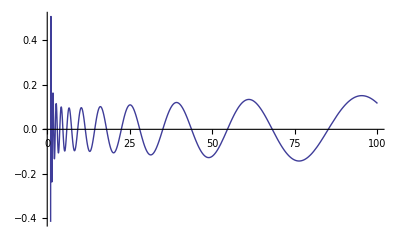

```mathematica
Plot[ Re[-Gamma[0,-Log[n] ZetaZero[1]]],{n,1,100}]
```

```mathematica
Limit[( - (-1)^z Gamma[z,-Log[n]]/Gamma[z])/z,z->1]
```

n

```mathematica
Limit[( (-1)^z- (-1)^z Gamma[z,-(ZetaZero[1])Log[n]]/Gamma[z] - 1)/z,z->1]
```

-2+n^ZetaZero[1]

```mathematica
Limit[( - (-1)^z Gamma[z,-(ZetaZero[-1])Log[n]]/Gamma[z])/z,z->1]
```

n^ZetaZero[-1]

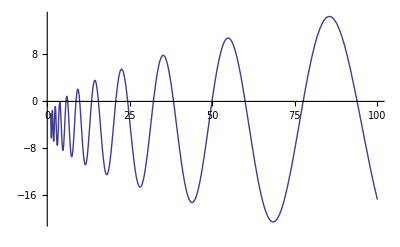

```mathematica
Plot[ n^ZetaZero[1]+n^ZetaZero[-1]-4,{n,1,100}]
```

```mathematica
Limit[( (-1)^z - (-1)^z Gamma[z,-(ZetaZero[1])Log[n]]/Gamma[z]-1)/z,z->2]
```

-1/2 Gamma[2,-Log[n] ZetaZero[1]]

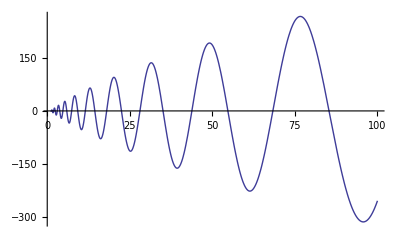

```mathematica
Plot[ Re[-1/2 Gamma[2,-Log[n] ZetaZero[1]]],{n,1,100}]
```

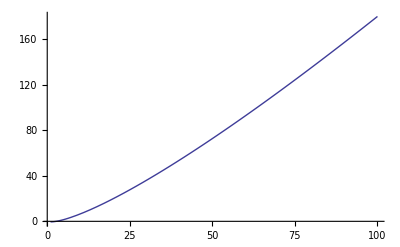

```mathematica
Plot[ Re[-1/2 Gamma[2,-Log[n] ]],{n,1,100}]
```

```mathematica
ff[n_,t_] := n-Sum[ n^ZetaZero[k]+n^ZetaZero[-k]+2,{k,1,200}]
```

```mathematica
N[ff[1000,60]]
```

218.909-5.68434×10^-14 ⅈ

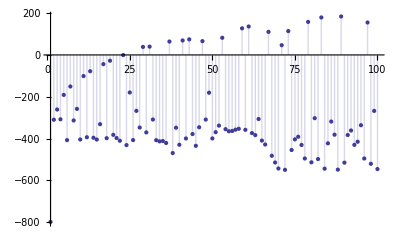

```mathematica
DiscretePlot[Re[ff[n,50]],{n,1,100}]
```